```mathematica
(*Constant, Fermi-Dirac and Fermi-Dirac changing with energy*)
K2meV=1000*8.617332478*10^−5;K2eV=8.617332478*10^−5;
fermiDirac[energy_,temp_]:=1/(Exp[energy/(K2eV*temp)]+1)

(*define sigma and kappa kernels*)
sigmaK[energy_,temp_]:=-D[fermiDirac[energy,temp],energy]
kappaK[energy_,temp_]:=-(1/temp)*(energy^2)*D[fermiDirac[energy,temp],energy]
```

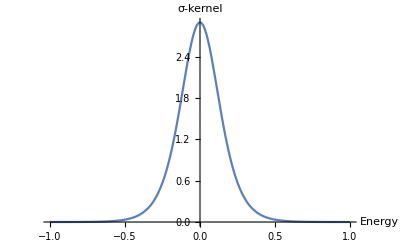

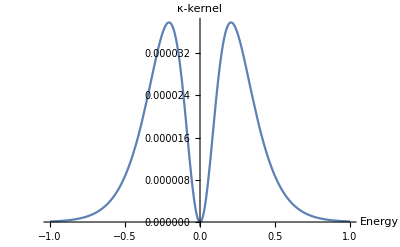

```mathematica
(*Plot Kernel for charge transport (sigma) and heat flux (kappa)*)
B=5;
Plot[Evaluate[sigmaK[energy,1000]],{energy,-B/5,B/5},PlotRange->All,AxesLabel->{"Energy","σ-kernel"}]
Plot[Evaluate[kappaK[energy,1000]],{energy,-B/5,B/5},PlotRange->All,AxesLabel->{"Energy","κ-kernel"}]
```

```mathematica
lorenz[energy_,temp_]:=N[Integrate[kappaK[energy,temp],energy]//Simplify,3]/(temp*N[Integrate[sigmaK[energy,temp],energy]//Simplify,3])
```

```mathematica
(Re@lorenz[energy,temp]/.{energy->-2,temp->100}//N)-(Re@lorenz[energy,temp]/.{energy->2,temp->100}//N)
```

-2.45518×10^97

```mathematica
lorenz[energy,100]
```

-0.01 (1.+2.72^(116.05 energy)) (energy ((0.01-0.01/(1.+2.72^(116. energy))) energy-0.000172 Log[1.+2.72^(116. energy)])-1.49×10^-6 PolyLog[2.,-1. 2.72^(116. energy)])

```mathematica
symDOS={Abs[energy^(1/2)]/NIntegrate[Abs[energy^(1/2)],{energy,-B,0}],Abs[energy]/NIntegrate[Abs[energy],{energy,-B,0}],Abs[energy^2]/NIntegrate[Abs[energy^(2)],{energy,-B,0}],Abs[2energy-4PDF[NormalDistribution[-1,0.2],energy]+4PDF[NormalDistribution[1,0.2],energy]]/(Integrate[Abs[2energy-4PDF[NormalDistribution[-1,0.2],energy]+4PDF[NormalDistribution[1,0.2],energy]],{energy,-B,0}])}
largeValDOS={(Abs[energy^(1/2)]+Ramp[2energy])/NIntegrate[(Abs[energy^(1/2)]+Ramp[2energy]),{energy,-B,0}],(Abs[energy^(1)]+Ramp[2energy])/NIntegrate[(Abs[energy^(1)]+Ramp[2energy]),{energy,-B,0}],(Abs[energy^(2)]+Ramp[2energy])/NIntegrate[(Abs[energy^(2)]+Ramp[2energy]),{energy,-B,0}],Abs[2energy-4PDF[NormalDistribution[-1,0.2],energy]]/(Integrate[Abs[2energy-4PDF[NormalDistribution[-1,0.2],energy]],{energy,-B,0}])}
symDOS+Ramp[2energy]
largeCondDOS={(Abs[energy^(1/2)]+Ramp[-2energy])/NIntegrate[(Abs[energy^(1/2)]+Ramp[-2energy]),{energy,-B,0}],(Abs[energy^(1)]+Ramp[-2energy])/NIntegrate[(Abs[energy^(1)]+Ramp[-2energy]),{energy,-B,0}],(Abs[energy^(2)]+Ramp[-2energy])/NIntegrate[(Abs[energy^(2)]+Ramp[-2energy]),{energy,-B,0}],Abs[2energy+4PDF[NormalDistribution[1,0.2],energy]]/(Integrate[Abs[2energy+4PDF[NormalDistribution[1,0.2],energy]],{energy,-B,0}])}
```

{0.134164 √Abs[energy],0.08 Abs[energy],0.024 Abs[energy]^2,0.03448276134745868771976373154575334220390101528 Abs[7.9788456080286535587989211986876373695171726232987 ⅇ^(-12.5 (-1+energy)^2)-7.9788456080286535587989211986876373695171726232987 ⅇ^(-12.5 (1+energy)^2)+2 energy]}

{0.134164 (√Abs[energy]+Ramp[2 energy]),0.08 (Abs[energy]+Ramp[2 energy]),0.024 (Abs[energy]^2+Ramp[2 energy]),0.03448275998407411754038805642705564439807289941281 Abs[-7.9788456080286535587989211986876373695171726232987 ⅇ^(-12.5 (1+energy)^2)+2 energy]}

{0.134164 √Abs[energy]+Ramp[2 energy],0.08 Abs[energy]+Ramp[2 energy],0.024 Abs[energy]^2+Ramp[2 energy],0.03448276134745868771976373154575334220390101528 Abs[7.9788456080286535587989211986876373695171726232987 ⅇ^(-12.5 (-1+energy)^2)-7.9788456080286535587989211986876373695171726232987 ⅇ^(-12.5 (1+energy)^2)+2 energy]+Ramp[2 energy]}

{0.0308133 (√Abs[energy]+Ramp[-2 energy]),0.0266667 (Abs[energy]+Ramp[-2 energy]),0.015 (Abs[energy]^2+Ramp[-2 energy]),0.0400000018338630996931652311651568249608784825135 Abs[7.9788456080286535587989211986876373695171726232987 ⅇ^(-12.5 (-1+energy)^2)+2 energy]}

```mathematica
GraphicsGrid[{Table[Plot[{symDOS[[i]],Evaluate@largeValDOS[[i]],Evaluate@largeCondDOS[[i]]},{energy,-4,4},PlotLegends->SwatchLegend[{"Symmetric","Large-val","Large-cond"}]],{i,1,4}]},ImageSize->1200]
```

-Graphics-

```mathematica
plotoptionsigma={"Sigma kernel times root DOS","Sigma kernel times linear DOS","Sigma kernel times squared DOS","Sigma kernel times linear + exp"};

plotoptionkappa={"Kappa kernel times root DOS","Kappa kernel times linear DOS","Kappa kernel times squared DOS","Kappa kernel times linear + exp"};
```

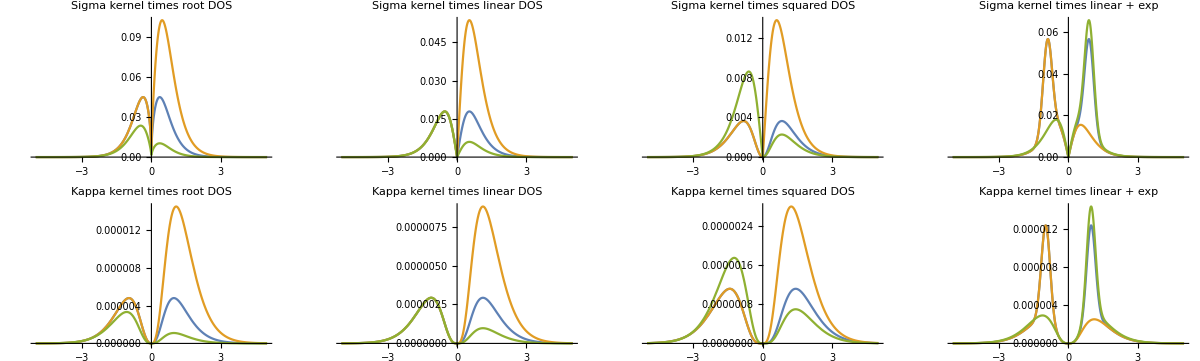

```mathematica
GraphicsGrid[{Table[Plot[{Evaluate[symDOS[[i]]*sigmaK[energy,4000]],Evaluate[largeValDOS[[i]]*sigmaK[energy,4000]],Evaluate[largeCondDOS[[i]]*sigmaK[energy,4000]]},{energy,-B,B},PlotRange->All,PlotLabel->Evaluate[plotoptionsigma[[i]]]],{i,1,4}],Table[Plot[{Evaluate[symDOS[[i]]*kappaK[energy,4000]],Evaluate[largeValDOS[[i]]*kappaK[energy,4000]],Evaluate[largeCondDOS[[i]]*kappaK[energy,4000]]},{energy,-B,B},PlotRange->All,PlotLabel->Evaluate[plotoptionkappa[[i]]]],{i,1,4
}]},ImageSize->1200]
```

```mathematica
sigmaT=Table[Table[NIntegrate[{Evaluate[symDOS[[i]]*sigmaK[energy,T]],Evaluate[largeValDOS[[i]]*sigmaK[energy,T]],Evaluate[largeCondDOS[[i]]*sigmaK[energy,T]]},{energy,-4B,4B}],{i,1,4}],{T,100,4000,100}];
kappaT=Table[Table[NIntegrate[{Evaluate[symDOS[[i]]*kappaK[energy,T]],Evaluate[largeValDOS[[i]]*kappaK[energy,T]],Evaluate[largeCondDOS[[i]]*kappaK[energy,T]]},{energy,-4B,4B}],{i,1,4}],{T,100,4000,100}];
temmps=Table[T,{T,100,4000,100}]
```

{100,200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000,2100,2200,2300,2400,2500,2600,2700,2800,2900,3000,3100,3200,3300,3400,3500,3600,3700,3800,3900,4000}

```mathematica
plotoptionsigma2={"Sigma - root DOS","Sigma - linear DOS","Sigma - squared DOS","Sigma - linear + exp"};
plotoptionkappa2={"Kappa - root DOS","Kappa - linear DOS","Kappa - squared DOS","Kappa - linear + exp"};
plotoptionsigmakappa={"Sigma/Kappa - root DOS","Sigma/Kappa - linear DOS","Sigma/Kappa - squared DOS","Sigma/Kappa - linear + exp"};
plotoptionlorenz={"Lorenz - root DOS","Lorenz - linear DOS","Lorenz - squared DOS","Lorenz - linear + exp"};
```

```mathematica
(*sigmaT[[temp]][[root,linear,square]][[symmetric,asymmetric]]*)
(*Transpose[Transpose[sigmaT][[root,linear,square]]][[symmetric,asymmetric]]*)
GraphicsGrid[{Table[ListPlot[Transpose[Transpose[sigmaT][[i]]],PlotLabel->Evaluate[plotoptionsigma2[[i]]],PlotLegends->SwatchLegend[{"symmetric","large val","large cond"}]],{i,1,4}]},ImageSize->1300]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListPlot[Transpose[Transpose[kappaT][[i]]],PlotLabel->Evaluate[plotoptionkappa2[[i]]],PlotLegends->SwatchLegend[{"symmetric","large val","large cond"}]],{i,1,4}]},ImageSize->1300]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListPlot[Transpose[Transpose[kappaT/sigmaT][[i]]],PlotLabel->Evaluate[plotoptionsigmakappa[[i]]],PlotLegends->SwatchLegend[{"symmetric","large val","large cond"}]],{i,1,4}]},ImageSize->1300]
```

-Graphics-

```mathematica
GraphicsGrid[{Table[ListPlot[Transpose[Transpose[kappaT/(sigmaT)][[i]]*temmps^-1],PlotLabel->Evaluate[plotoptionlorenz[[i]]],PlotLegends->SwatchLegend[{"symmetric","large val","large cond"}],PlotRange->{{0,40},{3.5*10^-8,1.2*10^-7}}],{i,1,4}]},ImageSize->1200]
```

-Graphics-

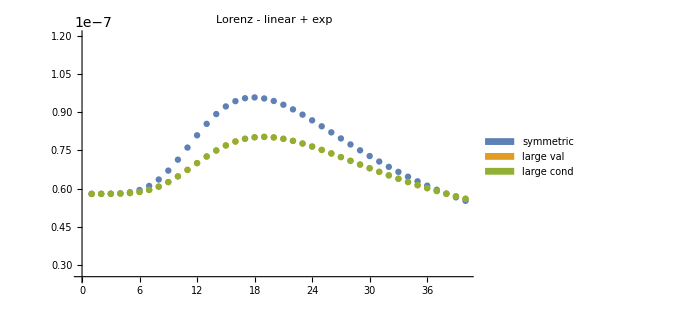

```mathematica
Show[Table[ListPlot[Transpose[Transpose[kappaT/(sigmaT)][[i]]*temmps^-1],PlotLabel->Evaluate[plotoptionlorenz[[i]]],PlotLegends->SwatchLegend[{"symmetric","large val","large cond"}],PlotRange->{{0,40},{2.5*10^-8,1.2*10^-7}},ImageSize->500],{i,4,4}]]
```

```mathematica
(Transpose[kappaT/(sigmaT)][[3]]*temmps^-1)[[1]]
```

{1.02844×10^-7,5.88455×10^-8,5.88455×10^-8}

```mathematica
n=3.992211760198622*^-8;
n1=5.795057886125392*^-8
n2=5.8845490077145*^-8
n3=1.0284386395639509*^-7
n*2/Pi//N
```

5.79506×10^-8

5.88455×10^-8

1.02844×10^-7

2.54152×10^-8

```mathematica
Solve[(n1/Pi)*x==2.45*10^-8,x]
```

{{x→1.32818}}

```mathematica
n1*4/(3Pi)
```

2.4595×10^-8

```mathematica
x/.{{x->1.3281837994617833}}
```

{1.32818}

```mathematica
n2*4/(3Pi)
```

2.49748×10^-8

```mathematica
n3*3/(4Pi)
```

2.45522×10^-8

4.8639